```mathematica
$Version
```

12.3.0 for Microsoft Windows (64-bit) (May 10, 2021)

[Note]
This code was further improved for locally averaged SFG spectra in SFG hyperspectral images  from the reference (J. Phys. Chem. B 2018, 122, 19, 5006–5019).

SFG mapping images and data processing

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

### A. input and data import

#### 1. Input

```mathematica
(*IR power values for normalization (experimentally measured) *)
Power2950=4.6;
Power3350=1.5;

(*SFG microscopy data collection setup*) (* 1024 data points in one spectrum, the area of 30 pixel by 30 pixel scanned with step distance of 10 μm *)
n=1024;
nx=30; (*# of row*)
ny=30; (*# of col*)
d=10;(*step distance*)
n nx ny (* check if the number matches with the length of data1&2 later*)

(*For plotting later*)
Table[-d*i,{i,0,nx}];
Table[-d*i,{i,0,ny}];
tickX=Table[-2d*i,{i,0,nx/2}];
tickY=Table[-2d*i,{i,0,ny/2}];
If[Length[tickX]>Length[tickY],tick=tickX,tick=tickY];
If[nx>=ny,imgSize=700,imgSize=300];
If[nx>=ny,legSize=220,legSize=440];
```

921600

#### 2. Data import

```mathematica
(*CH input*)
data1=Import["15mst pps O5 H 30x30(10)_ch_833.asc"];
Length[data1]
data1=Table[{data1[[i,1]],data1[[i,2]]/Power2950},{i,1,Length[data1]}];
(*OH input*)
data2=Import["15mst pps O5 H 30x30(10)_oh_832.asc"];
data2=Table[{data2[[i,1]],data2[[i,2]]/Power3350},{i,1,Length[data2]}];
data2//Length
(*Combine CH+OH*)
data3=Table[{data1[[i,1]],data1[[i,2]]+data2[[i,2]],0},{i,1,Length[data1]}];
raw=Table[{data3[[i,1]],data3[[i,2]]},{i,1,Length[data3]}];
raw//Dimensions
```

921600

921600

{921600,2}

### B. Data process

#### 1. Organize data into “e” table

```mathematica
i=1;
j=1;
k=1;
e=Table[Table[{0,0},{i,1,n}],{j,1,nx},{k,1,ny}];

While[k<ny+1,
j=1;
While[j<nx+1,
i=1;
While[i<n+1,
e[[j,k,i]]={raw[[((j-1)ny+(2Floor[(j+1)/2]-j)(k-1)+(2Floor[j/2]+1-j)(ny-k))n+i,1]],raw[[((j-1)ny+(2Floor[(j+1)/2]-j)(k-1)+(2Floor[j/2]+1-j)(ny-k))n+i,2]]};
i++];
j++];
k++]
```

```mathematica
(* e[[x,y]] gives full SFG spectra at a given pixel. Make sure the pixel used in the plot below exhists. *)
ListLinePlot[e[[1,1]],PlotRange->{{2700,3600},All},Frame->True,ImageSize->700,LabelStyle->{FontFamily->"Arial", FontSize->20,Black},FrameLabel->{"Wavenumber (1/cm)","SFG Intensity (a.u.)"}];
```

#### 2. Re-arrange “e” table into “c” table for mapping images --> Figure 1b or c

```mathematica
(* At a given wavenumber, c[[wvn]] gives (nx,ny,int.) data *)
i=1;
j=1;
k=1;

b=Table[Table[{-(j-1)d,-(k-1)d,e[[j,k,i,2]]},{j,1,nx},{k,1,ny}],{i,1,n}];

i=1;
c=Table[ArrayReshape[b[[i]],{nx ny,3}],{i,1,n}];
c[[287]]//Dimensions;

(* Define a function "SFGmap" that produce mapping images *)
SFGmap[wvn_]:=Module[{},

wvn1=e[[1,1,wvn,1]];
ListContourPlot[c[[wvn]],PlotRange->All,Frame->True,ImageSize->imgSize,LabelStyle->{FontFamily->"Arial", FontSize->16,Black},FrameLabel->{"x","y"},FrameTicks->{{tick,tick},{tick,tick}},AspectRatio->ny/nx,ColorFunction->"Rainbow",Contours->20,ContourStyle->Line,GridLines->{Range[-d*(nx-1),0,d],Range[-d*(ny-1),0,d]},Method->{"GridLinesInFront"->True}, PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->legSize,LegendLabel->"Intensity"],{After,Top}],PlotLabel->ToExpression["wvn1"]]
]
(* The argument "wvn" is the nth dataset that represent a certian wavenumber; 287 = 3320 cm^-1, and 449 = 2944 cm^-1. *)
```

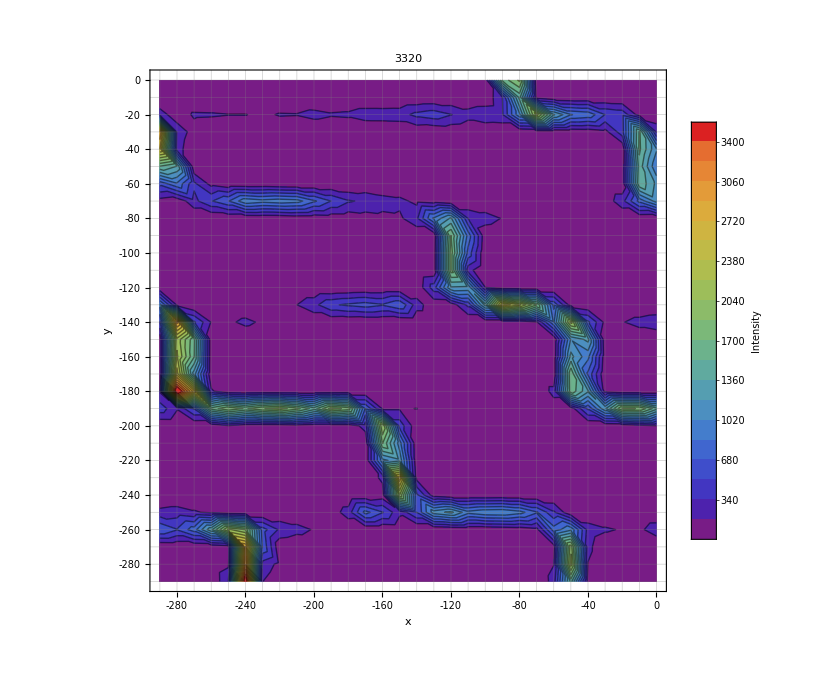
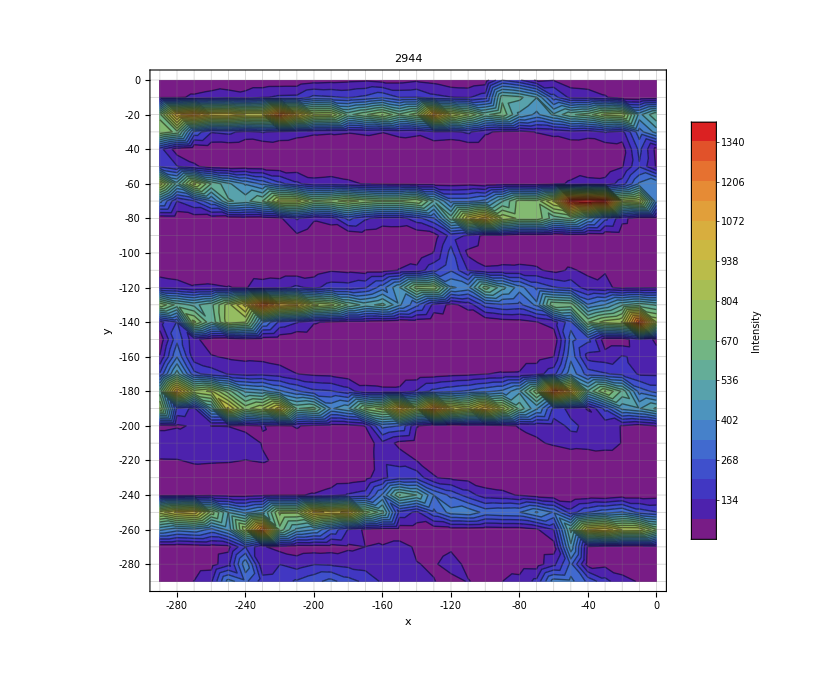

```mathematica
{SFGmap[287],SFGmap[448]}(*Check if the wavenumber on top of the SFG maps is what you want *)
```

Figure 1b --> 3320 cm^-1 map (The purple area was further removed )
-Graphics-

### C. Averaged SFG spectra

#### 1. Average over all pixels/coordinates in the SFG map

```mathematica
(* saved to "et" table, or Averaged plot -> "etp" directly *)
i=1;
j=1;
p=1;
et=Table[{e[[i,j,p,1]],Sum[e[[i,j,p,2]],{i,1,nx},{j,1,ny}]/(1.0 nx ny)},{p,1,n}];
etp:=Module[{},
ListLinePlot[et,PlotRange->{{2700,3600},All},Frame->True,ImageSize->700,LabelStyle->{FontFamily->"Arial", FontSize->20,Black},FrameLabel->{"Wavenumber (1/cm)","SFG Intensity (a.u.)"},PlotStyle-> ColorFunction->"Rainbow",GridLines->{{2870,2911,2924,2944,2970,3320},None},PlotLegends->Automatic]
]
```

#### Plot check --> Figure 1e or f

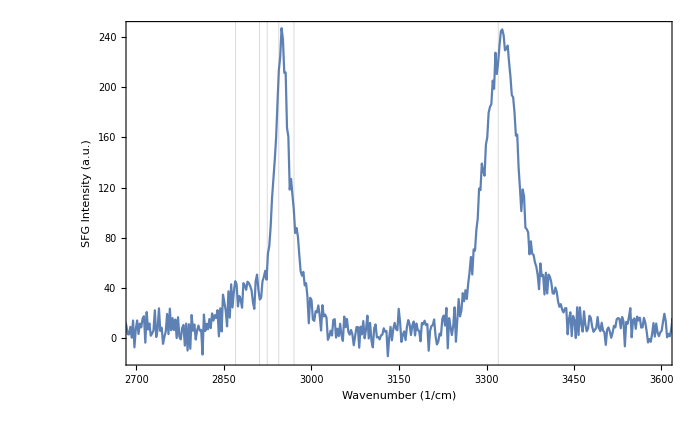
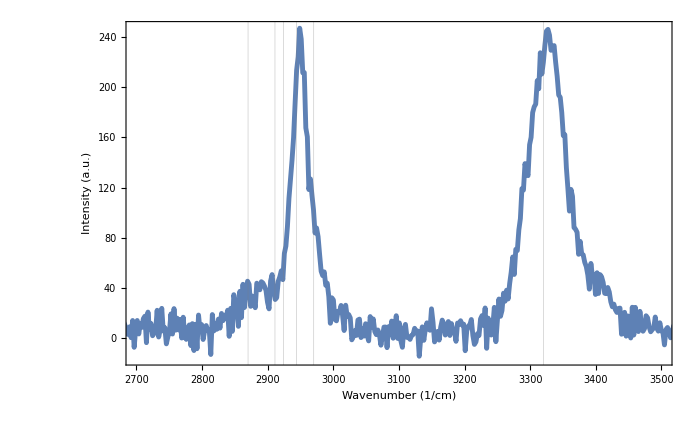

```mathematica
(* by "etp" or by "et" *) (*Average over the whole area is not meaningful for inhomogenouse samples *)
{etp,ListLinePlot[et,PlotRange->{{2700,3500},All},DataRange->{200,450},Frame->True,ImageSize->700,LabelStyle->{FontFamily->"Arial", FontSize->20,Black},FrameLabel->{"Wavenumber (1/cm)","Intensity (a.u.)"},PlotStyle->{Thickness[0.005]},GridLines->{{2870,2911,2924,2944,2970,3320},None}]}
```

#### 2. Average over specific regions (region 1-n)

```mathematica
(*Give the average SFG spectrum of a rectangulr area surrounded by x=x1, x=x2, y=y1, and y=y2*)
region[x1_,x2_,y1_,y2_]:=
Module[{},
ClearAll[regiont];
i=1;
j=1;
p=1;
regiont=Table[{e[[i,j,p,1]],0},{p,1,n}];
While[p<n+1,
sum=0;
count=0;
For[i=(x1/d)+1,i≤(x2/d)+1,i++,
For[j=(y1/d)+1,j≤ (y2/d)+1,j++,
sum=sum+e[[i,j,p,2]];count++;
]
];
regiont[[p,2]]=N[sum/count];
p++];
count
]
```

#### Areas are manually assigned t tables “r1~rn” *Note that the negative signs are removed from the coordinates in the SFG map.

The red/blue/green area in the Figure 1d below were analyzed (average) by manually typing the four coordinates.
-Graphics-

```mathematica
(*r1-20 are H regions  *)
region[110,260,20,20];
r1=regiont;
region[20,50,20,20];
r2=regiont;
region[140,250,70,70];
r3=regiont;

region[30,100,70,80];
r4=regiont;
region[160,260,130,130];
r5=regiont;
region[70,100,120,130];
r6=regiont;

region[0,30,130,140];
r7=regiont;

region[190,250,180,190];
r8=regiont;
region[80,140,190,190];
r9=regiont;
region[0,30,180,190];
r10=regiont;
region[260,290,250,260];
r11=regiont;

region[170,220,250,250];
r12=regiont;
region[70,120,250,250];
r13=regiont;
region[0,30,260,260];
r14=regiont;
```

```mathematica
(*r21-40 are V regions*)
region[10,10,30,60];
r21=regiont;
region[120,120,80,110];
r22=regiont;
region[270,280,140,170];
r23=regiont;
region[40,50,140,170];
r24=regiont;
region[150,160,200,230];
r25=regiont;

region[240,240,270,290];
r26=regiont;

region[50,50,260,290];
r27=regiont;
```

```mathematica
(*r41-60 are F regions*)
region[50,220,40,50];
r41=regiont;
region[160,280,90,100];
r42=regiont;
region[0,90,100,100];
r43=regiont;
region[80,220,150,160];
r44=regiont;
region[190,290,210,230];
r45=regiont;
region[0,110,210,230];
r46=regiont;

region[90,190,270,280];
r47=regiont;
```

#### Plot smoothening

```mathematica
MAn=3;(*Moving average*)

(*et series*)
MAet=MovingAverage[et,MAn];

(*region series*)
MAr1=MovingAverage[r1,MAn];
MAr2=MovingAverage[r2,MAn];
MAr3=MovingAverage[r3,MAn];
MAr4=MovingAverage[r4,MAn];
MAr5=MovingAverage[r5,MAn];
MAr6=MovingAverage[r6,MAn];
MAr7=MovingAverage[r7,MAn];
MAr8=MovingAverage[r8,MAn];
MAr9=MovingAverage[r9,MAn];
MAr10=MovingAverage[r10,MAn];
MAr11=MovingAverage[r11,MAn];
MAr12=MovingAverage[r12,MAn];
MAr13=MovingAverage[r13,MAn];
MAr14=MovingAverage[r14,MAn];

MAr21=MovingAverage[r21,MAn];
MAr22=MovingAverage[r22,MAn];
MAr23=MovingAverage[r23,MAn];
MAr24=MovingAverage[r24,MAn];
MAr25=MovingAverage[r25,MAn];
MAr26=MovingAverage[r26,MAn];
MAr27=MovingAverage[r27,MAn];

MAr41=MovingAverage[r41,MAn];
MAr42=MovingAverage[r42,MAn];
MAr43=MovingAverage[r43,MAn];
MAr44=MovingAverage[r44,MAn];
MAr45=MovingAverage[r45,MAn];
MAr46=MovingAverage[r46,MAn];
MAr47=MovingAverage[r47,MAn];
```

#### Plot check --> Figure 1e or f

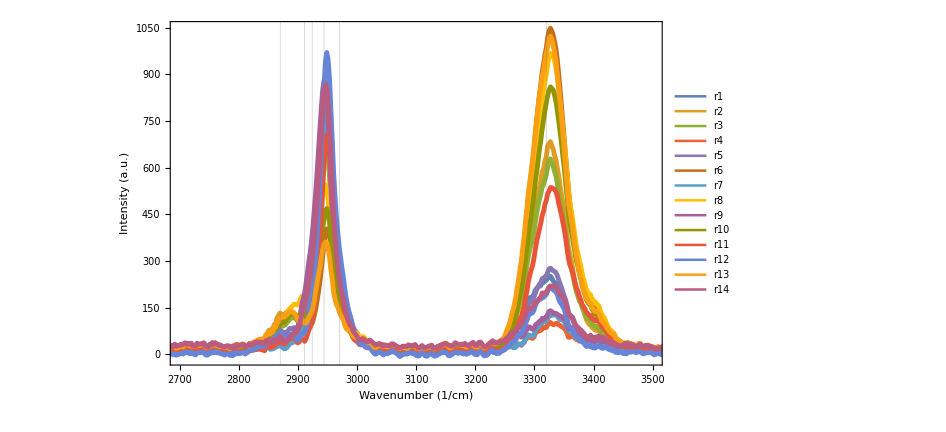
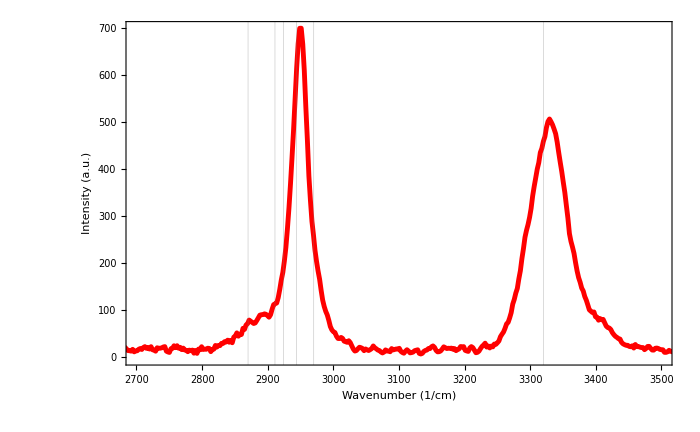

```mathematica
(*H*)
Hregions={MAr1,MAr2,MAr3,MAr4,MAr5,MAr6,MAr7,MAr8,MAr9,MAr10,MAr11,MAr12,MAr13,MAr14};
AvgHr=Table[{r1[[p,1]],1/Length[Hregions](MAr1[[p,2]]+MAr2[[p,2]]+MAr3[[p,2]]+MAr4[[p,2]]+MAr5[[p,2]]+MAr6[[p,2]]+MAr7[[p,2]]+MAr8[[p,2]]+MAr9[[p,2]]+MAr10[[p,2]]+MAr11[[p,2]]+MAr12[[p,2]]+MAr13[[p,2]]+MAr14[[p,2]])},{p,1,n-MAn+1}];

{
(*H regions*)
ListLinePlot[Hregions,PlotRange->{{2700,3500},All},DataRange->{200,450},Frame->True,ImageSize->700,LabelStyle->{FontFamily->"Arial", FontSize->20,Black},PlotStyle->{Thickness[0.005]},FrameLabel->{"Wavenumber (1/cm)","Intensity (a.u.)"},GridLines->{{2870,2911,2924,2944,2970,3320},None},PlotLegends->{"r1","r2","r3","r4","r5","r6","r7","r8","r9","r10","r11","r12","r13","r14","r15","r16","r17","r18"}],
(*Average of H regions*)
ListLinePlot[AvgHr,PlotRange->{{2700,3500},All},DataRange->{200,450},Frame->True,ImageSize->700,LabelStyle->{FontFamily->"Arial", FontSize->20,Black},PlotStyle->Directive[Thickness[0.005],Red],FrameLabel->{"Wavenumber (1/cm)","Intensity (a.u.)"},GridLines->{{2870,2911,2924,2944,2970,3320},None}]
}
```

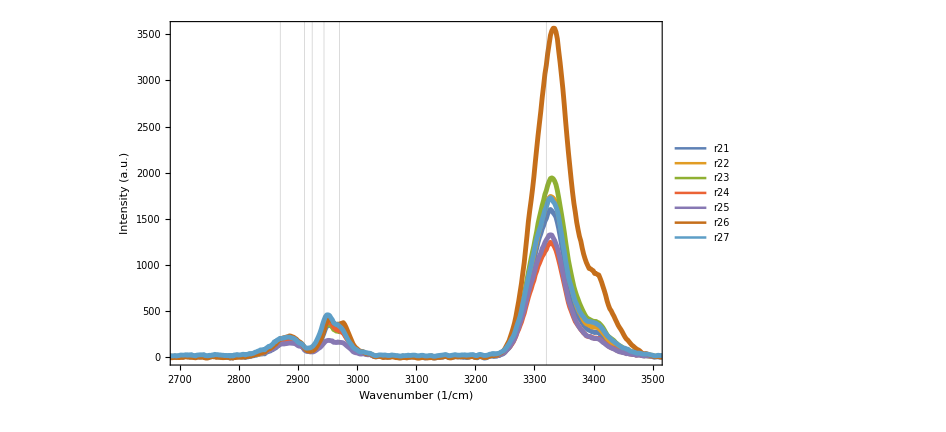
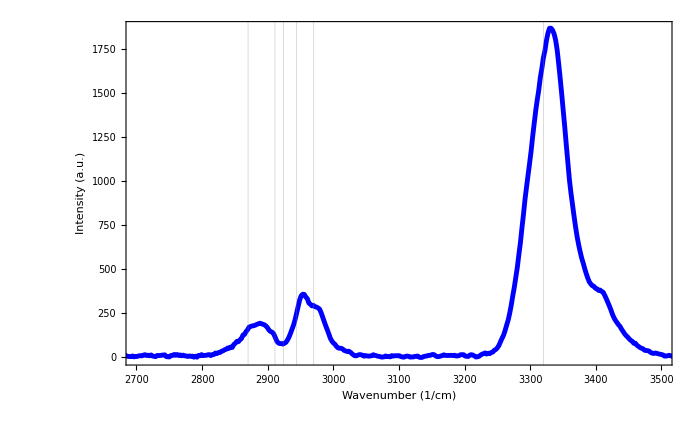

```mathematica
(*V*)
Vregions={MAr21,MAr22,MAr23,MAr24,MAr25,MAr26,MAr27};
AvgVr=Table[{r21[[p,1]],1/Length[Vregions](MAr21[[p,2]]+MAr22[[p,2]]+MAr23[[p,2]]+MAr24[[p,2]]+MAr25[[p,2]]+MAr26[[p,2]]+MAr27[[p,2]])},{p,1,n-MAn+1}];
{
(*V regions*)
ListLinePlot[Vregions,PlotRange->{{2700,3500},All},DataRange->{200,450},Frame->True,ImageSize->700,LabelStyle->{FontFamily->"Arial", FontSize->20,Black},PlotStyle->{Thickness[0.005]},FrameLabel->{"Wavenumber (1/cm)","Intensity (a.u.)"},GridLines->{{2870,2911,2924,2944,2970,3320},None},PlotLegends->{"r21","r22","r23","r24","r25","r26","r27","r28","r29","r30","r31","r32"}],
(*Average of V regions*)
ListLinePlot[AvgVr,PlotRange->{{2700,3500},All},DataRange->{200,450},Frame->True,ImageSize->700,LabelStyle->{FontFamily->"Arial", FontSize->20,Black},PlotStyle->Directive[Thickness[0.005],Blue],FrameLabel->{"Wavenumber (1/cm)","Intensity (a.u.)"},GridLines->{{2870,2911,2924,2944,2970,3320},None}]
}
```

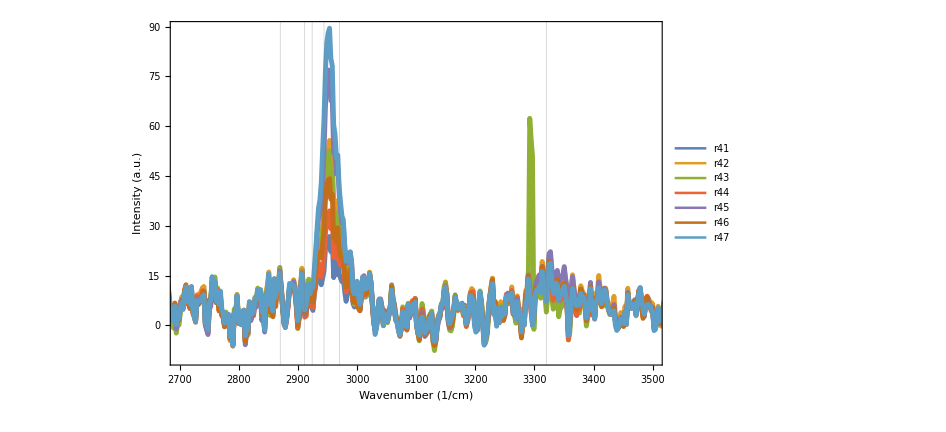
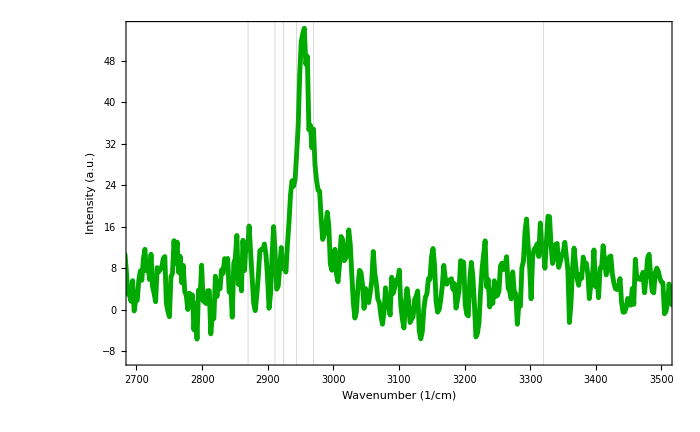

```mathematica
(*F*)
Fregions={MAr41,MAr42,MAr43,MAr44,MAr45,MAr46,MAr47};
AvgFr=Table[{r41[[p,1]],1/Length[Fregions](MAr41[[p,2]]+MAr42[[p,2]]+MAr43[[p,2]]+MAr44[[p,2]]+MAr45[[p,2]]+MAr46[[p,2]]+MAr47[[p,2]])},{p,1,n-MAn+1}];
{
(*F regions*)
ListLinePlot[Fregions,PlotRange->{{2700,3500},All},DataRange->{200,450},Frame->True,ImageSize->700,LabelStyle->{FontFamily->"Arial", FontSize->20,Black},PlotStyle->{Thickness[0.005]},FrameLabel->{"Wavenumber (1/cm)","Intensity (a.u.)"},GridLines->{{2870,2911,2924,2944,2970,3320},None},PlotLegends->{"r41","r42","r43","r44","r45","r46","r47"}],
(*Average of F regions*)
ListLinePlot[AvgFr,PlotRange->{{2700,3500},All},DataRange->{200,450},Frame->True,ImageSize->700,LabelStyle->{FontFamily->"Arial", FontSize->20,Black},PlotStyle->Directive[Thickness[0.005],Darker[Green]],FrameLabel->{"Wavenumber (1/cm)","Intensity (a.u.)"},GridLines->{{2870,2911,2924,2944,2970,3320},None}]
}
```

### D. Data export

```mathematica
(*Organize and save the generated data to tables "etSeries", "regionSeries", and "avgRSeries"*)
(*The error message saying "Part" can be ignored*)
etSeries=Table[{MAet[[i,1]],MAet[[i,2]]},{i,1,n-MAn+1}];
etSeries=PrependTo[etSeries,{"wavenumber","Avg over the whole"}];
(**)
regionSeries=Table[{MAr1[[i,1]],
MAr1[[i,2]],MAr2[[i,2]],MAr3[[i,2]],MAr4[[i,2]],MAr5[[i,2]],MAr6[[i,2]],MAr7[[i,2]],MAr8[[i,2]],MAr9[[i,2]],MAr10[[i,2]],
MAr11[[i,2]],MAr12[[i,2]],MAr13[[i,2]],MAr14[[i,2]],MAr15[[i,2]],MAr16[[i,2]],MAr17[[i,2]],MAr18[[i,2]],MAr19[[i,2]],MAr20[[i,2]],
MAr21[[i,2]],MAr22[[i,2]],MAr23[[i,2]],MAr24[[i,2]],MAr25[[i,2]],MAr26[[i,2]],MAr27[[i,2]],MAr28[[i,2]],MAr29[[i,2]],MAr30[[i,2]],
MAr31[[i,2]],MAr32[[i,2]],MAr33[[i,2]],MAr34[[i,2]],MAr35[[i,2]],MAr36[[i,2]],MAr37[[i,2]],MAr38[[i,2]],MAr39[[i,2]],MAr40[[i,2]],
MAr41[[i,2]],MAr42[[i,2]],MAr43[[i,2]],MAr44[[i,2]],MAr45[[i,2]],MAr46[[i,2]],MAr47[[i,2]],MAr48[[i,2]],MAr49[[i,2]],MAr50[[i,2]],
MAr51[[i,2]],MAr52[[i,2]],MAr53[[i,2]],MAr54[[i,2]],MAr55[[i,2]],MAr56[[i,2]],MAr57[[i,2]],MAr58[[i,2]],MAr59[[i,2]],MAr60[[i,2]]
},{i,1,n-MAn+1}];
regionSeries=PrependTo[regionSeries,{"wavenumber","r1","r2","r3","r4","r5","r6","r7","r8","r9","r10","r11","r12","r13","r14","r15","r16","r17","r18","r19","r20","r21","r22","r23","r24","r25","r26","r27","r28","r29","r30","r31","r32","r33","r34","r35","r36","r37","r38","r39","r40","r41","r42","r43","r44","r45","r46","r47","r48","r49","r50","r51","r52","r53","r54","r55","r56","r57","r58","r59","r60"}];

(**)
avgRSeries=Table[{MAr1[[i,1]],AvgHr[[i,2]],AvgVr[[i,2]],AvgFr[[i,2]]},{i,1,n-MAn+1}];
avgRSeries=PrependTo[avgRSeries,{"wavenumber","avg of H regions","avg of V regions","avg of F regions"}];

(*Export*)
name=CurrentValue[EvaluationNotebook[],{"NotebookFileName"}];
name=StringDrop[name,-3];
Export[NotebookDirectory[]<>ToExpression["name"]<>ToString["_"]<>"avgall.csv",etSeries]
Export[NotebookDirectory[]<>ToExpression["name"]<>ToString["_"]<>"regions 1-n.csv",regionSeries]
Export[NotebookDirectory[]<>ToExpression["name"]<>ToString["_"]<>"avgHVF.csv",avgRSeries]
(*The error message here can be ignored*)
```

Part::partd: Part specification MAr15⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification MAr16⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification MAr17⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

C:\Users\jongc\OneDrive - The Pennsylvania State University\$ Priority\$ O figures - Nat. comm\$Code and Sofrware\for zip\SFGmap\Onion epidermis Horizontal_avgall.csv

C:\Users\jongc\OneDrive - The Pennsylvania State University\$ Priority\$ O figures - Nat. comm\$Code and Sofrware\for zip\SFGmap\Onion epidermis Horizontal_regions 1-n.csv

C:\Users\jongc\OneDrive - The Pennsylvania State University\$ Priority\$ O figures - Nat. comm\$Code and Sofrware\for zip\SFGmap\Onion epidermis Horizontal_avgHVF.csv